## INFO :

## Read in .dat files :

```mathematica
(*myFolder = "C:\\Users\\Charlotte\\Dropbox (Personal)\\_copy_old lab NB notes\\"
```

```mathematica
myFolder = "/Users/ccialek/Dropbox (Personal)/_copy_old lab NB notes"
```

/Users/ccialek/Dropbox (Personal)/_copy_old lab NB notes

```mathematica
myNT2=<<(myFolder<>"/102017_Imaging_14-5h_results_NT.dat");
myTA2=<<(myFolder<>"/102017_Imaging_14-5h_results_TA.dat");
myTL2=<<(myFolder<>"/102017_Imaging_14-5h_results_TL.dat");
myTA1=<<(myFolder<>"/1004-517_Imaging_14-5h_results2_TA.dat");
myNT1=<<(myFolder<>"/1004-517_Imaging_14-5h_results2_NT.dat");
myTA3=<<(myFolder<>"/120317_Imaging_14-5h_results_TA.dat");
myNT3=<<(myFolder<>"/120317_Imaging_14-5h_results_NT.dat");
myTL3=<<(myFolder<>"/120317_Imaging_14-5h_results_TL.dat");
```

```mathematica
(*
myNT -> 18, 13,25
myTA -> 13, 18, 26
myTL ->  , 13, 18
*)
```

```mathematica
myTL2//Dimensions
myTL3//Dimensions
```

{13,7,1}

{18,2,1}

## Import data

```mathematica
cellsNT1 = myNT1[[All,1]];
cellsNT2 = myNT2[[All,1]];
cellsNT3 = myNT3[[All,1]];
cellsTA1 = myTA1[[All,1]];
cellsTA2 = myTA2[[All,1]];
cellsTA3 = myTA3[[All,1]];
cellsTL2 = myTL2[[All,1]];
cellsTL3 = myTL3[[All,1]];
```

```mathematica
rnaNT1 = myNT1[[All,2,1,2;;All]];
rnaNT2 = myNT2[[All,2,1,2;;All]];
rnaTA1 = myTA1[[All,2,1,2;;All]];
rnaTA2 = myTA2[[All,2,1,2;;All]];
rnaTL2 = myTL2[[All,2,1,2;;All]];
```

```mathematica
transNT1 = myNT1[[All,3,1,2;;All]];
transNT2 = myNT2[[All,3,1,2;;All]];
transTA1 = myTA1[[All,3,1,2;;All]];
transTA2 = myTA2[[All,3,1,2;;All]];
transTL2 = myTL2[[All,3,1,2;;All]];
```

```mathematica
accumNT1 = myNT1[[All,4,1,2;;All]];
accumNT2 = myNT2[[All,4,1,2;;All]];
accumTA1 = myTA1[[All,4,1,2;;All]];
accumTA2 = myTA2[[All,4,1,2;;All]];
accumTL2 = myTL2[[All,4,1,2;;All]];
accumNT3 = myNT3[[All,2,1,2;;All]];
accumTL3 = myTL3[[All,2,1,2;;All]];
accumTA3 = myTA3[[All,2,1,2;;All]];
```

```mathematica
sickNT1 = myNT1[[All,5,1,2;;All]];
sickNT2 = myNT2[[All,5,1,2;;All]];
sickTA1 = myTA1[[All,5,1,2;;All]];
sickTA2 = myTA2[[All,5,1,2;;All]];
sickTL2 = myTL2[[All,5,1,2;;All]];
```

```mathematica
agoNT1 = myNT1[[All,6,1,2;;All]];
agoNT2 = myNT2[[All,6,1,2;;All]];
agoTA1 = myTA1[[All,6,1,2;;All]];
agoTA2 = myTA2[[All,6,1,2;;All]];
agoTL2 = myTL2[[All,6,1,2;;All]];
```

```mathematica
tethNT1 = myNT1[[All,7,1,2;;All]];
tethNT2 = myNT2[[All,7,1,2;;All]];
tethTA1 = myTA1[[All,7,1,2;;All]];
tethTA2 = myTA2[[All,7,1,2;;All]];
tethTL2 = myTL2[[All,7,1,2;;All]];
```

```mathematica
times = rnaNT1[[1,All,1]]
```

{4.,6.,8.,10.,15.,20.}

## Graphs

### Graphs...

#### RNA :

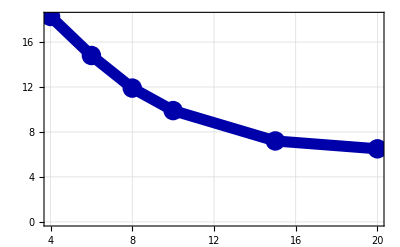

Part::partw: Part 6 of {{4.,10.},{6.,12.},{8.,32.},{10.,58.},{15.,23.}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

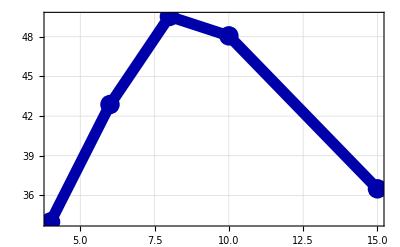

{{4.,26.1364},{6.,28.8375},{8.,30.7167},{10.,28.9833},{15.,21.85}}

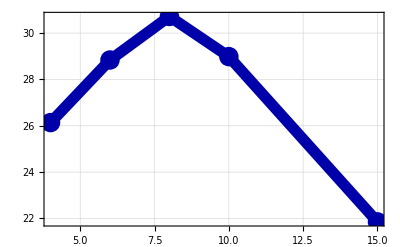

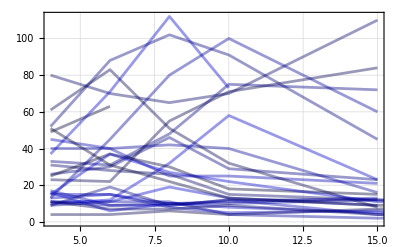

```mathematica
prnaTA1=rnaTA1//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
AvgrnaTA1=Cases[Table[Mean[Cases[rnaTA1[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgrnaTA1=AvgrnaTA1//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
prnaTA2=rnaTA2//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
AvgrnaTA2=Cases[Table[Mean[Cases[rnaTA2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgrnaTA2=AvgrnaTA2//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
totalAvgrnaTA=Table[Mean[{AvgrnaTA2[[i]],AvgrnaTA1[[i]]}],{i,1,Length@AvgrnaTA2,1}]
ptotalAvgrnaTA=totalAvgrnaTA//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
prnaTA = Show[prnaTA2,prnaTA1]
```

```mathematica
prnaTL2=rnaTL2//ListPlot[#,PlotStyle->Table[{RGBColor[0,1-j/10,0],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgrnaTL2=Cases[Table[Mean[Cases[rnaTL2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgrnaTL2=AvgrnaTL2//ListPlot[#,PlotStyle->{Darker[Green],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
prnaTL = Show[prnaTL2]
```

-Graphics-

Part::partw: Part 6 of {{4.,91.},{6.,101.},{8.,},{10.,},{15.,}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

-Graphics-

-Graphics-

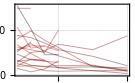

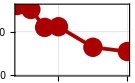

Part::partw: Part 6 of {{4.,13.},{6.,17.},{8.,18.},{10.,7.},{15.,}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

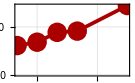

{{4.,36.3763},{6.,36.4056},{8.,34.2813},{10.,35.0192},{15.,38.5625}}

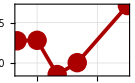

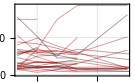

```mathematica
prnaNT1=rnaNT1//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgrnaNT1=Cases[Table[Mean[Cases[rnaNT1[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgrnaNT1=AvgrnaNT1//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
prnaNT2=rnaNT2//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
AvgrnaNT2=Cases[Table[Mean[Cases[rnaNT2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgrnaNT2=AvgrnaNT2//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
totalAvgrnaNT=Table[Mean[{AvgrnaNT2[[i]],AvgrnaNT1[[i]]}],{i,1,Length@AvgrnaNT2,1}]
ptotalAvgrnaNT=totalAvgrnaNT//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
prnaNT = Show[prnaNT2,prnaNT1]
```

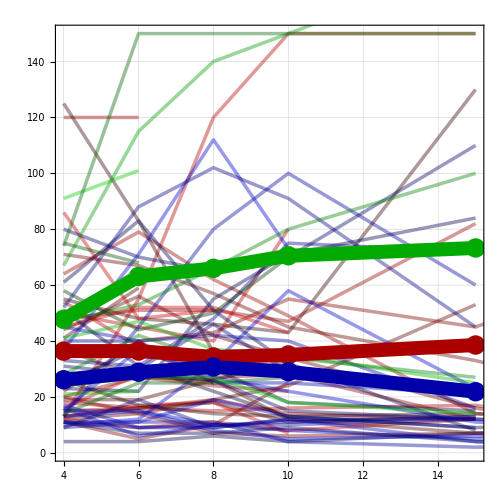

```mathematica
Show[prnaNT,prnaTA,prnaTL,ptotalAvgrnaNT,ptotalAvgrnaTA,pAvgrnaTL2,AspectRatio->1]
```

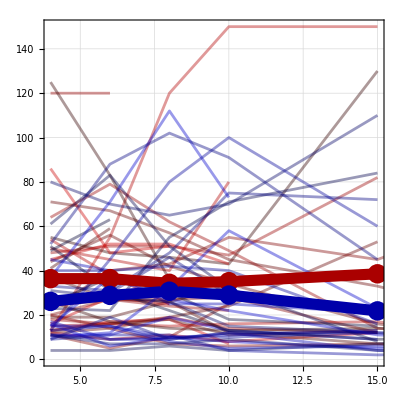

```mathematica
Show[prnaNT,prnaTA,ptotalAvgrnaNT,ptotalAvgrnaTA,PlotRange->{{4,15},{0,150}},AspectRatio->1]
```

#### %Translation :

```mathematica
ptransTA1=transTA1//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgtransTA1=Cases[Table[Mean[Cases[transTA1[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtransTA1=AvgtransTA1//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
ptransTA2=transTA2//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgtransTA2=Cases[Table[Mean[Cases[transTA2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtransTA2=AvgtransTA2//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
totalAvgtransTA=Table[Mean[{AvgtransTA2[[i]],AvgtransTA1[[i]]}],{i,1,Length@AvgtransTA2,1}];
ptotalAvgtransTA=totalAvgtransTA//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
ptransTA = Show[ptransTA2,ptransTA1]
```

-Graphics-

-Graphics-

-Graphics-

Part::partw: Part 6 of {{4.,0.1},{6.,0.416667},{8.,0.15625},{10.,0.137931},{15.,0.0434783}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

-Graphics-

-Graphics-

-Graphics-

```mathematica
ptransTL=transTL2//ListPlot[#,PlotStyle->Table[{RGBColor[0,1-j/10,0],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgtransTL2=Cases[Table[Mean[Cases[transTL2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2]
pAvgtransTL2=AvgtransTL2//ListPlot[#,PlotStyle->{Darker[Green],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

-Graphics-

Part::partw: Part 6 of {{4.,0.901099},{6.,0.970297},{8.,},{10.,},{15.,}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

{{4.,0.556632},{6.,0.565412},{8.,0.458124},{10.,0.247129},{15.,0.145635}}

-Graphics-

```mathematica
ptransNT1=transNT1//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgtransNT1=Cases[Table[Mean[Cases[transNT1[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtransNT1=AvgtransNT1//ListPlot[#,PlotStyle->{Red,Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
ptransNT2=transNT2//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgtransNT2=Cases[Table[Mean[Cases[transNT2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtransNT2=AvgtransNT2//ListPlot[#,PlotStyle->{Red,Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
totalAvgtransNT=Table[Mean[{AvgtransNT2[[i]],AvgtransNT1[[i]]}],{i,1,Length@AvgtransNT2,1}]
ptotalAvgtransNT=totalAvgtransNT//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
ptransNT = Show[ptransNT1,ptransNT2]
```

-Graphics-

-Graphics-

-Graphics-

Part::partw: Part 6 of {{4.,0.692308},{6.,0.647059},{8.,0.611111},{10.,0.571429},{15.,}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

-Graphics-

{{4.,0.749776},{6.,0.769071},{8.,0.774227},{10.,0.710656},{15.,0.401452}}

-Graphics-

-Graphics-

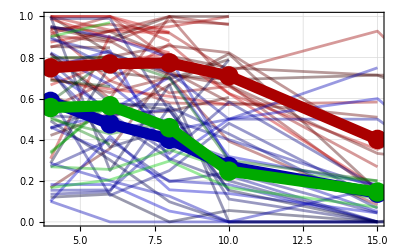

```mathematica
Show[ptransNT,ptransTA,ptransTL,ptotalAvgtransNT,ptotalAvgtransTA,pAvgtransTL2,PlotRange->{{4,15},{0,1}}]
```

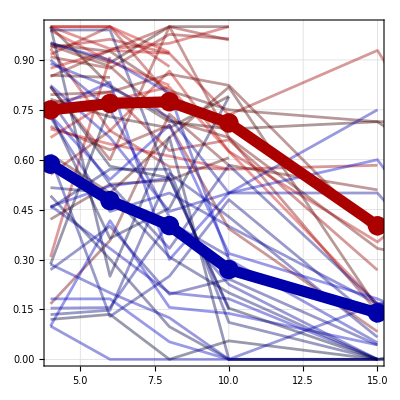

```mathematica
Show[ptransNT,ptransTA,ptotalAvgtransNT,ptotalAvgtransTA,PlotRange->{{4,15},{0,1}},AspectRatio->1]
```

#### # Tethered :

```mathematica
ptethTA1=tethTA1//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgtethTA1=Cases[Table[Mean[Cases[tethTA1[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtethTA1=AvgtethTA1//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
ptethTA2=tethTA2//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgtethTA2=Cases[Table[Mean[Cases[tethTA2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtethTA2=AvgtethTA2//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
totalAvgtethTA=Table[Mean[{AvgtethTA2[[i]],AvgtethTA1[[i]]}],{i,1,Length@AvgtethTA2,1}]
ptotalAvgtethTA=totalAvgtethTA//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
Show[ptethTA2,ptethTA1]
```

-Graphics-

-Graphics-

-Graphics-

Part::partw: Part 6 of {{4.,2.},{6.,5.},{8.,5.},{10.,15.},{15.,17.}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

-Graphics-

{{4.,11.0833},{6.,16.3176},{8.,19.4625},{10.,16.0333},{15.,10.9214}}

-Graphics-

-Graphics-

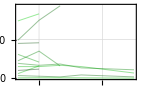

Part::partw: Part 6 of {{4.,89.},{6.,100.},{8.,},{10.,},{15.,}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

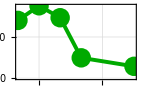

```mathematica
ptethTL=tethTL2//ListPlot[#,PlotStyle->Table[{RGBColor[0,1-j/10,0],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgtethTL=Cases[Table[Mean[Cases[tethTL2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtethTL=AvgtethTL//ListPlot[#,PlotStyle->{Darker[Green],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

```mathematica
ptethNT1=tethNT1//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgtethNT1=Cases[Table[Mean[Cases[tethNT1[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtethNT1=AvgtethNT1//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
ptethNT2=tethNT2//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.005],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
AvgtethNT2=Cases[Table[Mean[Cases[tethNT2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtethNT2=AvgtethNT2//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
totalAvgtethNT=Table[Mean[{AvgtethNT2[[i]],AvgtethNT1[[i]]}],{i,1,Length@AvgtethNT2,1}]
ptotalAvgtethNT=totalAvgtethNT//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
ptethNT = Show[ptethNT2,ptethNT1]
```

-Graphics-

-Graphics-

Part::partw: Part 6 of {{4.,1.},{6.,1.},{8.,1.},{10.,1.},{15.,}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

-Graphics-

{{4.,0.208333},{6.,0.227273},{8.,0.227273},{10.,0.227273},{15.,1.25}}

-Graphics-

-Graphics-

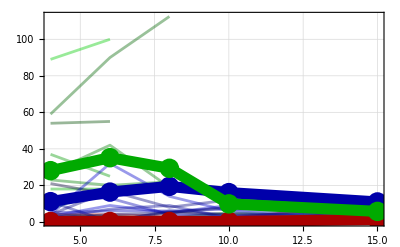

```mathematica
Show[ptethTL,ptethNT,ptethTA1,ptotalAvgtethNT,ptotalAvgtethTA,pAvgtethTL]
```

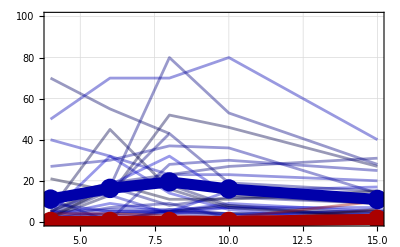

```mathematica
Show[ptethTA1,ptethTA2,ptethNT1,ptethNT2,ptotalAvgtethNT,ptotalAvgtethTA,PlotRange->{{4,15},{0,100}}]
```

#### % cy3 accumulation :

```mathematica
paccumTA1=accumTA1//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.0025],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgaccumTA1=Cases[Table[Mean[Cases[accumTA1[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtethTA1=AvgaccumTA1//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
paccumTA2=accumTA2//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.0025],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgaccumTA2=Cases[Table[Mean[Cases[accumTA2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgaccumTA2=AvgaccumTA2//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
paccumTA3=accumTA3//ListPlot[#,PlotStyle->Table[{RGBColor[0,0,1-j/10],Thickness[0.0025],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgaccumTA3=Cases[Table[Mean[Cases[accumTA3[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgtethTA3=AvgaccumTA3//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
totalAvgaccumTA=Table[Mean[{AvgaccumTA2[[i]],AvgaccumTA3[[i]],AvgaccumTA1[[i]]}],{i,1,Length@AvgaccumTA2,1}]
ptotalAvgaccumTA=totalAvgaccumTA//ListPlot[#,PlotStyle->{Darker[Blue],Thickness[0.015]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
paccumTA=Show[paccumTA3,paccumTA2,paccumTA1]
```

-Graphics-

-Graphics-

-Graphics-

Part::partw: Part 6 of {{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.05}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

-Graphics-

-Graphics-

Part::partw: Part 6 of {{4.,0.05},{6.,0.},{8.,0.},{10.,0.},{15.,0.}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

-Graphics-

{{4.,0.0789015},{6.,0.0812821},{8.,0.0864286},{10.,0.0996978},{15.,0.137201}}

-Graphics-

-Graphics-

```mathematica
StandardDeviation/@{AvgaccumTA1,AvgaccumTA2,AvgaccumTA3}
```

{{5.99166,0.0200859},{4.219,0.078208},{4.219,0.0131172}}

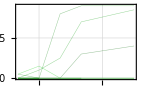

Part::partw: Part 6 of {{4.,0.},{6.,0.},{8.,},{10.,},{15.,}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

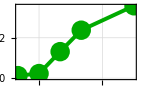

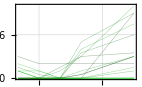

Part::partw: Part 6 of {{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

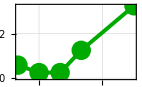

{{4.,0.0354167},{6.,0.0238636},{8.,0.078125},{10.,0.18125},{15.,0.341667}}

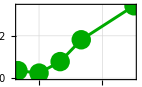

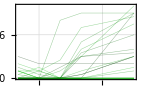

```mathematica
paccumTL2=accumTL2//ListPlot[#,PlotStyle->Table[{RGBColor[0,1-j/10,0],Thickness[0.0025],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgaccumTL2=Cases[Table[Mean[Cases[accumTL2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgaccumTL2=AvgaccumTL2//ListPlot[#,PlotStyle->{Darker[Green],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
paccumTL3=accumTL3//ListPlot[#,PlotStyle->Table[{RGBColor[0,1-j/10,0],Thickness[0.0025],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgaccumTL3=Cases[Table[Mean[Cases[accumTL3[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgaccumTL3=AvgaccumTL3//ListPlot[#,PlotStyle->{Darker[Green],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
totalAvgaccumTL=Table[Mean[{AvgaccumTL2[[i]],AvgaccumTL3[[i]]}],{i,1,Length@AvgaccumTA2,1}]
ptotalAvgaccumTL=totalAvgaccumTL//ListPlot[#,PlotStyle->{Darker[Green],Thickness[0.015]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
paccumTL = Show[paccumTL3,paccumTL2]
```

```mathematica
paccumNT1=accumNT1//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.0025],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgaccumNT1=Cases[Table[Mean[Cases[accumNT1[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgaccumNT1=AvgaccumNT1//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
paccumNT2=accumNT2//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.0025],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
AvgaccumNT2=Cases[Table[Mean[Cases[accumNT2[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgaccumNT2=AvgaccumNT2//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
paccumNT3=accumNT3//ListPlot[#,PlotStyle->Table[{RGBColor[1-j/10,0,0],Thickness[0.0025],Opacity[0.4]},{j,2,8,1}],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
AvgaccumNT3=Cases[Table[Mean[Cases[accumNT1[[All,i]],x_/;NumericQ[x⟦2⟧]]],{i,1,Length[times],1}],x_/;Length[x]==2];
pAvgaccumNT3=AvgaccumNT3//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
totalAvgaccumNT=Table[Mean[{AvgaccumNT2[[i]],AvgaccumNT3[[i]],AvgaccumNT1[[i]]}],{i,1,Length@AvgaccumNT2,1}]
ptotalAvgaccumNT=totalAvgaccumNT//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.015]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
paccumNT = Show[paccumNT2,paccumNT1,paccumNT3]
```

-Graphics-

-Graphics-

Part::partw: Part 6 of {{4.,0.1},{6.,0.1},{8.,0.},{10.,0.},{15.,}} does not exist.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::partd: Part specification 6⟦2⟧ is longer than depth of object.

-Graphics-

-Graphics-

-Graphics-

{{4.,0.0501684},{6.,0.0823232},{8.,0.172054},{10.,0.280808},{15.,0.499632}}

-Graphics-

-Graphics-

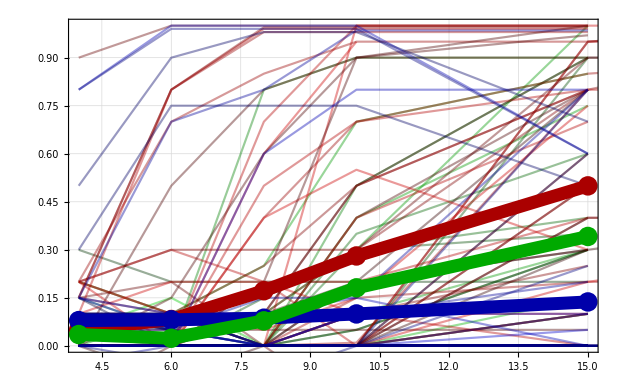

```mathematica
Show[paccumTL,paccumNT,paccumTA,ptotalAvgaccumNT,ptotalAvgaccumTA,ptotalAvgaccumTL,PlotRange->{{4,15},{0,1}}]
```

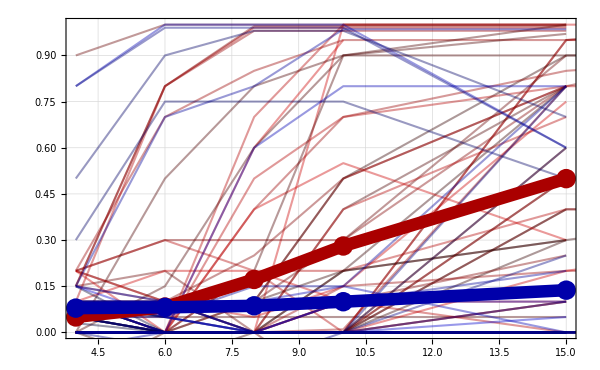

```mathematica
Show[paccumNT,paccumTA,ptotalAvgaccumNT,ptotalAvgaccumTA,PlotRange->{{4,15},{0,1}},ImageSize->600]
```

```mathematica
(*   standardError[ts_]:=StandardDeviation[ts]/Sqrt[ts["PathLength"]]
```

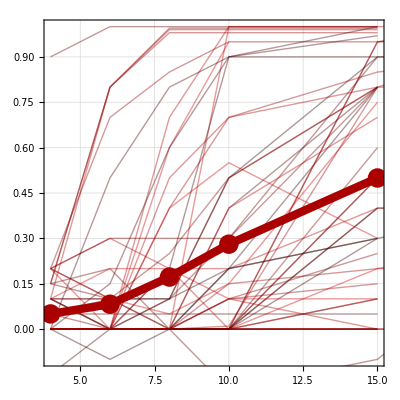

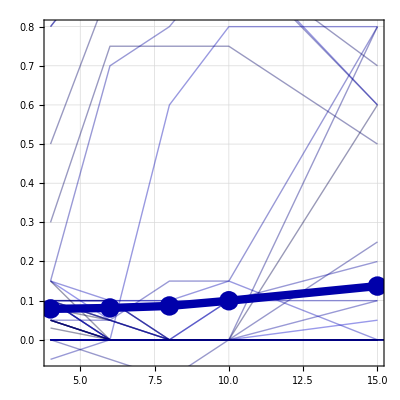

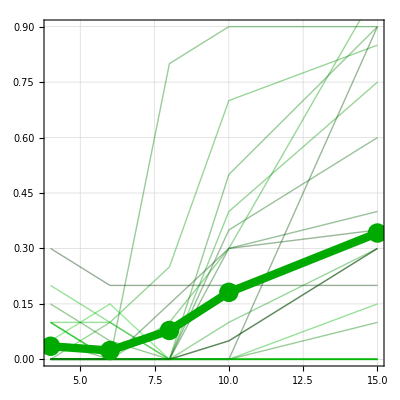

```mathematica
Show[paccumNT2,paccumNT1,paccumNT3,ptotalAvgaccumNT, PlotRange->{{4,15},{-.1,1}},AspectRatio->1]
Show[paccumTA2,paccumTA1,paccumTA3,ptotalAvgaccumTA, AspectRatio->1]
Show[paccumTL2,paccumTL3,ptotalAvgaccumTL, AspectRatio->1]
```

```mathematica
devAccumTA = StandardDeviation/@Table[{AvgaccumTA1[[j,2]],AvgaccumTA2[[j,2]],AvgaccumTA3[[j,2]]},{j,1,Length@AvgaccumTA2,1}]
devAccumNT = StandardDeviation/@Table[{AvgaccumNT1[[j,2]],AvgaccumNT2[[j,2]],AvgaccumNT3[[j,2]]},{j,1,Length@AvgaccumNT2,1}]
devAccumTL = StandardDeviation/@Table[{AvgaccumTL2[[j,2]],AvgaccumTL3[[j,2]]},{j,1,Length@AvgaccumTL2,1}]
```

{0.0412543,0.0577555,0.0764085,0.0869484,0.129914}

{0.0237647,0.0594846,0.0820829,0.10541,0.102522}

{0.0324091,0.00160706,0.0751301,0.0795495,0.0235702}

```mathematica
errorAccumTA = ;
errorAccumNT = ;
errorAccumTL = ;
```

## Binning based on #RNA in cell at frame # (choose 2, 3, 4, 5, or 6)

```mathematica
NTdata = Join[myNT1, myNT2];
TAdata = Join[myTA1, myTA2];
TLdata = Join[myTL2];
```

```mathematica
(*
m = 20
n = 80
o = 3
NTdataL=Cases[NTdata,x_/;x[[2,1,o,2]]<m];
NTdataM=Cases[NTdata,x_/;m≤x[[2,1,o,2]]≤n];
NTdataH=Cases[NTdata,x_/;n<x[[2,1,o,2]]];
TAdataL=Cases[TAdata,x_/;x[[2,1,o,2]]<m];
TAdataM=Cases[TAdata,x_/;m≤x[[2,1,o,2]]≤n];
TAdataH=Cases[TAdata,x_/;n<x[[2,1,o,2]]];
TLdataL=Cases[TLdata,x_/;x[[2,1,o,2]]<m];
TLdataM=Cases[TLdata,x_/;m≤x[[2,1,o,2]]≤n];
TLdataH=Cases[TLdata,x_/;n<x[[2,1,o,2]]];
*)
```

```mathematica
rmNTdata = NTdata//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
rmTLdata = TLdata//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
rmTAdata = TAdata//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
```

```mathematica
m = 20;
n = 60;
o = 4;
p=2;
NTdata0= rmNTdata//Cases[#,x_/; Head[x⟦p,1,o,2⟧]== String]&;
NTdataL= rmNTdata//Cases[#,x_/; x⟦p,1,o,2⟧< m]&;
NTdataM= rmNTdata//Cases[#,x_/; m≤ x⟦p,1,o,2⟧≤n]&;
NTdataH= rmNTdata//Cases[#,x_/; n< x⟦p,1,o,2⟧]&;
TAdata0= rmTAdata//Cases[#,x_/;  Head[x⟦p,1,o,2⟧]== String]&;
TAdataL=TAdata//Cases[#,x_/;  x⟦p,1,o,2⟧< m]&;
TAdataM= rmTAdata//Cases[#,x_/;  m≤x⟦p,1,o,2⟧≤ n]&;
TAdataH= rmTAdata//Cases[#,x_/;  n<x⟦p,1,o,2⟧]&;
TLdata0= rmTLdata//Cases[#,x_/; Head[x⟦p,1,o,2⟧]== String]&;
TLdataL=TLdata//Cases[#,x_/;   x⟦p,1,o,2⟧<m]&;
TLdataM= rmTLdata//Cases[#,x_/;  m≤x⟦p,1,o,2⟧≤n]&;
TLdataH= rmTLdata//Cases[#,x_/;  n<x⟦p,1,o,2⟧]&;
```

```mathematica
(*
NTdata0= rmNTdata/.""->0.//Cases[#,x_/; Head[x⟦p,1,o,2⟧]== String]&;
NTdataL= rmNTdata/.""->0.//Cases[#,x_/; x⟦p,1,o,2⟧< m]&;
NTdataM= rmNTdata/.""->0.//Cases[#,x_/; m≤ x⟦p,1,o,2⟧≤n]&;
NTdataH= rmNTdata/.""->0.//Cases[#,x_/; n< x⟦p,1,o,2⟧]&;
TAdata0= rmTAdata/.""->0.//Cases[#,x_/;  Head[x⟦p,1,o,2⟧]== String]&;
TAdataL=TAdata/.""->0.//Cases[#,x_/;  x⟦p,1,o,2⟧< m]&;
TAdataM= rmTAdata/.""->0.//Cases[#,x_/;  m≤x⟦p,1,o,2⟧≤ n]&;
TAdataH= rmTAdata/.""->0.//Cases[#,x_/;  n<x⟦p,1,o,2⟧]&;
TLdata0= rmTLdata/.""->0.//Cases[#,x_/; Head[x⟦p,1,o,2⟧]== String]&;
TLdataL=TLdata/.""->0.//Cases[#,x_/;   x⟦p,1,o,2⟧<m]&;
TLdataM= rmTLdata/.""->0.//Cases[#,x_/;  m≤x⟦p,1,o,2⟧≤n]&;
TLdataH= rmTLdata/.""->0.//Cases[#,x_/;  n<x⟦p,1,o,2⟧]&;
*)
```

```mathematica
NTdata[[5,2,1,2,2]]
```

44.

```mathematica
NTdata[[All,2,1,o,2]]
```

{25.,15.,62.,43.,42.,26.,14.,52.,40.,,10.,57.,,36.,51.,25.,24.,7.,18.,120.,19.,,,18.,46.,11.,,51.,27.,19.,26.}

```mathematica
Row[{"TA  ",Length@TAdata ,"   inc " ,Length@TAdata0,"   lo " ,Length@TAdataL ,"   med " ,Length@TAdataM ,"   hi " ,Length@TAdataH}]
Row[{"NT  ",Length@NTdata ,"   inc " ,Length@NTdata0,"   lo " ,Length@NTdataL ,"   med " ,Length@NTdataM ,"   hi " ,Length@NTdataH}]
Row[{"TL  ",Length@TLdata ,"   inc " ,Length@TLdata0,"   lo " ,Length@TLdataL ,"    med " ,Length@TLdataM ,"    hi " ,Length@TLdataH}]
```

TA  31   inc 4   lo 10   med 11   hi 2

NT  31   inc 3   lo 9   med 15   hi 2

TL  13   inc 4   lo 0    med 5    hi 3

### Graphs...

#### RNA :

```mathematica
prnaTAL = 
TAdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTAM = 
TAdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTAH = 
TAdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
```

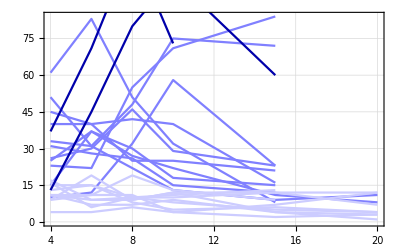

```mathematica
prnaTA = Show[prnaTAM,prnaTAL, prnaTAH]
```

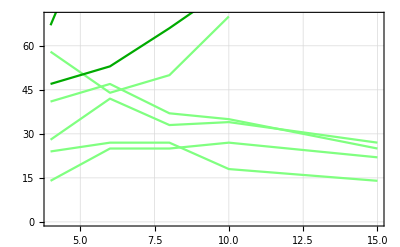

```mathematica
prnaTLL = 
TLdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTLM = 
TLdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTLH = 
TLdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTL = Show[prnaTLM,prnaTLL, prnaTLH]
```

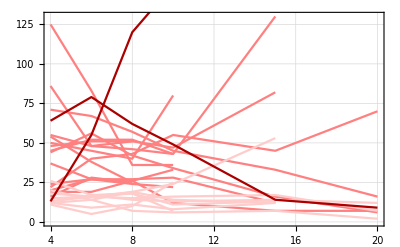

```mathematica
prnaNTL = 
NTdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNTM = 
NTdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNTH = 
NTdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNT = Show[prnaNTM,prnaNTL, prnaNTH]
```

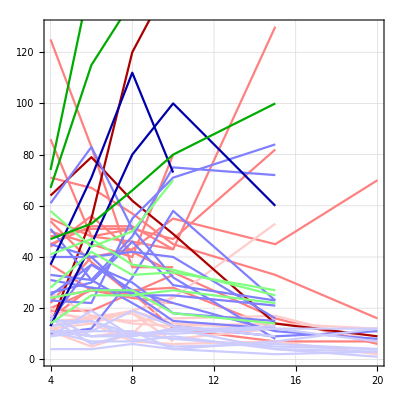

```mathematica
Show[prnaNT,prnaTA,prnaTL,AspectRatio->1]
```

#### %Translation :

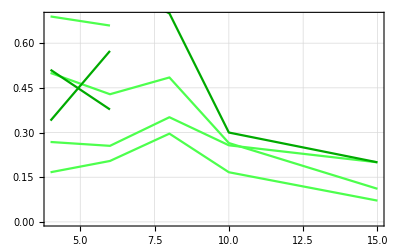

```mathematica
ptransTLL=TLdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTLM=TLdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTLH=TLdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTL = Show[ptransTLM,ptransTLL, ptransTLH]
```

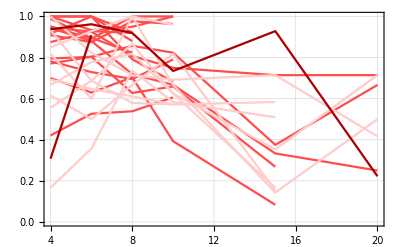

```mathematica
ptransNTL=NTdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNTM=NTdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNTH=NTdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNT = Show[ptransNTM,ptransNTL, ptransNTH]
```

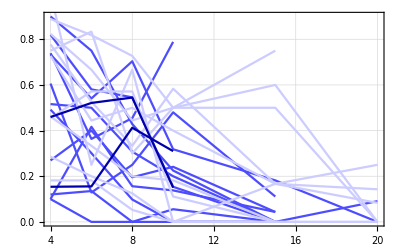

```mathematica
ptransTAL=TAdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTAM=TAdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTAH=TAdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTA = Show[ptransTAM,ptransTAL, ptransTAH]
```

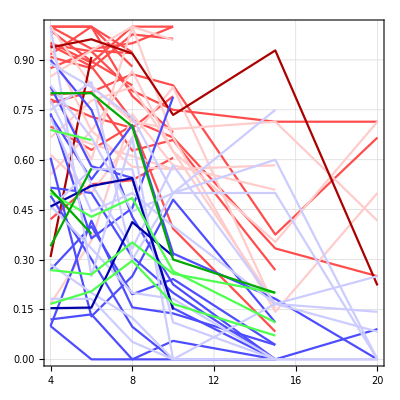

```mathematica
Show[ptransNT,ptransTA,ptransTL,AspectRatio->1]
```

#### # Tethered :

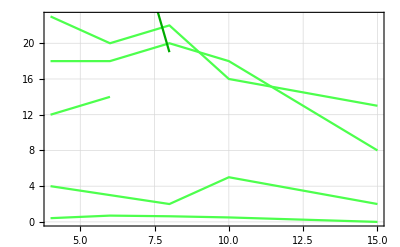

```mathematica
ptethTLL=TLdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTLM=TLdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTLH=TLdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTL = Show[ptethTLM,ptethTLL, ptethTLH]
```

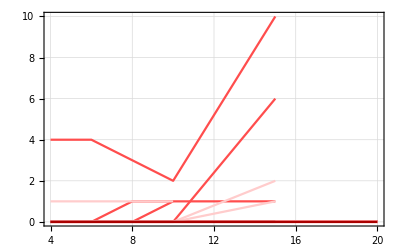

```mathematica
ptethNTL=NTdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNTM=NTdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNTH=NTdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNT = Show[ptethNTM,ptethNTL, ptethNTH]
```

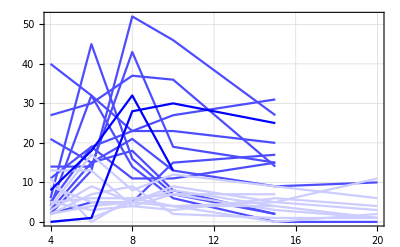

```mathematica
ptethTAL=TAdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTAM=TAdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTAH=TAdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Blue,Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTA = Show[ptethTAM,ptethTAL, ptethTAH]
```

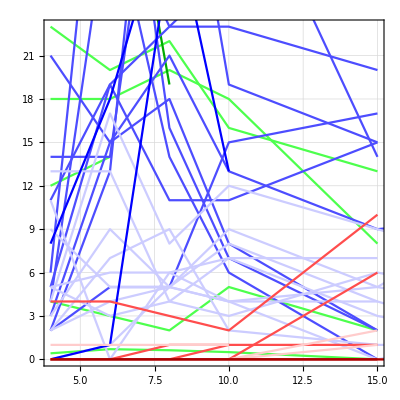

```mathematica
Show[ptethTL,ptethTA,ptethNT,AspectRatio->1]
```

#### % cy3 accumulation :

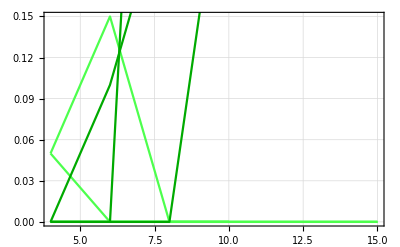

```mathematica
paccumTLL=TLdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTLM=TLdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTLH=TLdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTL = Show[paccumTLM,paccumTLL, paccumTLH]
```

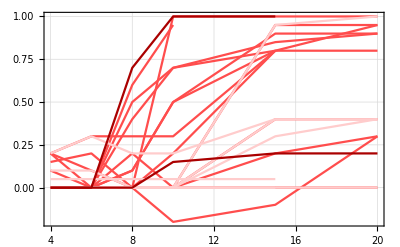

```mathematica
paccumNTL=NTdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumNTM=NTdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumNTH=NTdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumNT = Show[paccumNTM,paccumNTL, paccumNTH]
```

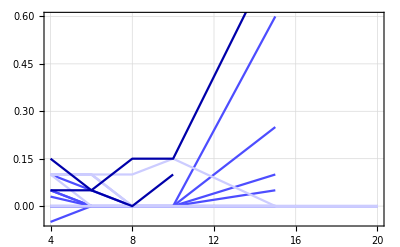

```mathematica
paccumTAL=TAdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTAM=TAdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTAH=TAdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTA = Show[paccumTAM,paccumTAL, paccumTAH]
```

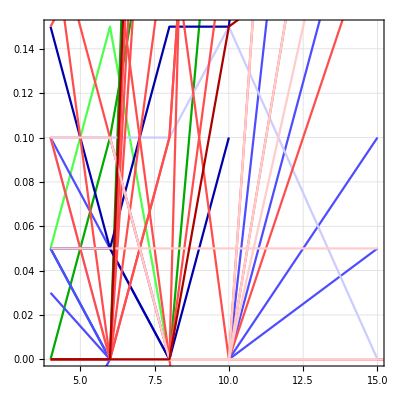

```mathematica
Show[paccumTL,paccumTA,paccumNT,AspectRatio->1]
```

### Totals :

Binned by # RNA per cell at Frame 4 : <20,  20-80,  <80

TA  31   inc 4   lo 10   med 11   hi 2

NT  31   inc 3   lo 9   med 15   hi 2

TL  13   inc 4   lo 0    med 5    hi 3

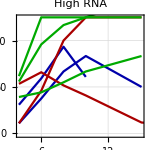
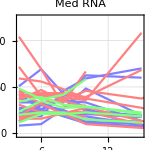
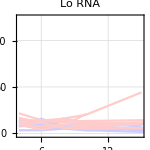

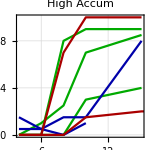
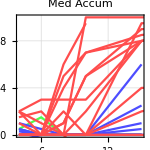
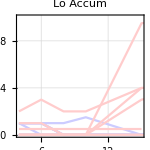

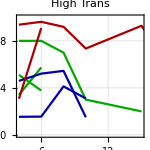
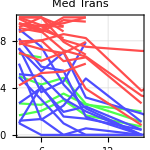

```mathematica
Row[{StringForm["Binned by # RNA per cell at Frame `` : <20,  20-80,  <80   ",o]}]
Row[{"TA  ",Length@TAdata ,"   inc " ,Length@TAdata0,"   lo " ,Length@TAdataL ,"   med " ,Length@TAdataM ,"   hi " ,Length@TAdataH}]
Row[{"NT  ",Length@NTdata ,"   inc " ,Length@NTdata0,"   lo " ,Length@NTdataL ,"   med " ,Length@NTdataM ,"   hi " ,Length@NTdataH}]
Row[{"TL  ",Length@TLdata ,"   inc " ,Length@TLdata0,"   lo " ,Length@TLdataL ,"    med " ,Length@TLdataM ,"    hi " ,Length@TLdataH}]
Row[{Show[prnaTAH,prnaNTH,prnaTLH,AspectRatio->1,PlotLabel->"High RNA",PlotRange->{{4,15},{-2,150}},ImageSize->150],
Show[prnaTAM,prnaNTM,prnaTLM,AspectRatio->1,PlotLabel->"Med RNA",PlotRange->{{4,15},{-2,150}},ImageSize->150],
Show[prnaTLL,prnaTAL,prnaNTL,prnaTLL,AspectRatio->1,PlotLabel->"Lo RNA",PlotRange->{{4,15},{-2,150}},ImageSize->150]
}]
Row[{Show[paccumTLH,paccumTAH,paccumNTH,AspectRatio->1,PlotLabel->"High Accum",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[paccumTLM,paccumTAM,paccumNTM,AspectRatio->1,PlotLabel->"Med Accum",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[paccumTLL,paccumTAL,paccumNTL,AspectRatio->1,PlotLabel->"Lo Accum",PlotRange->{{4,15},{0,1}},ImageSize->150]
}]
Row[{Show[ptransTLH,ptransTAH,ptransNTH,AspectRatio->1,PlotLabel->"High Trans",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[ptransTLM,ptransTAM,ptransNTM,AspectRatio->1,PlotLabel->"Med Trans",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[ptransTLL,ptransTAL,ptransNTL,AspectRatio->1,PlotLabel->"Lo Trans",PlotRange->{{4,15},{0,1}},ImageSize->150]
}]

(*
Row[{"***NOTE, the drop to 0 is sometimes bc the cell can't be quantified anymore!   "}]
*)
```

### Graph the %accumulation at 10h for HML w a scatter plot

```mathematica
accumNTL= Table[NTdataL[[i,4,1,5]]/. 10.->RandomReal[{.9,1.1}],{i,1,Length@NTdataL,1}];
accumNTM= Table[NTdataM[[i,4,1,5]]/. 10.->RandomReal[{.9,1.1}],{i,1,Length@NTdataM,1}];
accumNTH= Table[NTdataH[[i,4,1,5]]/. 10.->RandomReal[{.9,1.1}],{i,1,Length@NTdataH,1}];accumTLL= Table[TLdataL[[i,4,1,5]]/. 10.->RandomReal[{1.9,2.1}],{i,1,Length@TLdataL,1}];
accumTLM= Table[TLdataM[[i,4,1,5]]/. 10.->RandomReal[{1.9,2.1}],{i,1,Length@TLdataM,1}];
accumTLH= Table[TLdataH[[i,4,1,5]]/. 10.->RandomReal[{1.9,2.1}],{i,1,Length@TLdataH,1}];
accumTAL= Table[TAdataL[[i,4,1,5]]/. 10.->RandomReal[{2.9,3.1}],{i,1,Length@TAdataL,1}];
accumTAM= Table[TAdataM[[i,4,1,5]]/. 10.->RandomReal[{2.9,3.1}],{i,1,Length@TAdataM,1}];
accumTAH= Table[TAdataH[[i,4,1,5]]/. 10.->RandomReal[{2.9,3.1}],{i,1,Length@TAdataH,1}];
```

```mathematica
accumTLall = Join[accumTLL, accumTLM, accumTLH];
accumTAall = Join[accumTAL, accumTAM, accumTAH];
accumNTall = Join[accumNTL, accumNTM, accumNTH];
```

#### % cy3 accumulation :

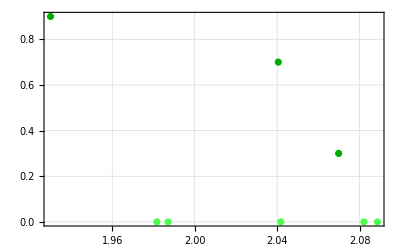

```mathematica
paccumTLL=accumTLL//ListPlot[#,PlotStyle->Lighter[Green,.8],PlotTheme->"Detailed",PlotRange->All]&;
paccumTLM=accumTLM//ListPlot[#,PlotStyle->Lighter[Green,.3],PlotTheme->"Detailed",PlotRange->All]&;
paccumTLH=accumTLH//ListPlot[#,PlotStyle->Darker[Green],PlotTheme->"Detailed",PlotRange->All]&;
paccumTL = Show[paccumTLM,paccumTLL, paccumTLH,PlotRange-> All]
```

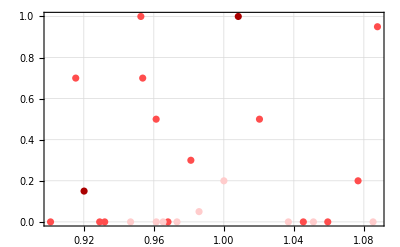

```mathematica
paccumNTL=accumNTL//ListPlot[#,PlotStyle->Lighter[Red,.8],PlotTheme->"Detailed",PlotRange->All]&;
paccumNTM=accumNTM//ListPlot[#,PlotStyle->Lighter[Red,.3],PlotTheme->"Detailed",PlotRange->All]&;
paccumNTH=accumNTH//ListPlot[#,PlotStyle->Darker[Red],PlotTheme->"Detailed",PlotRange->All]&;
paccumNT = Show[paccumNTM,paccumNTL, paccumNTH, PlotRange-> {0,1}]
```

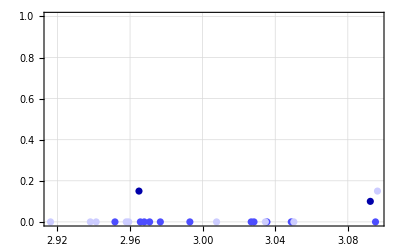

```mathematica
paccumTAL=accumTAL//ListPlot[#,PlotStyle->Lighter[Blue,.8],PlotTheme->"Detailed",PlotRange->All]&;
paccumTAM=accumTAM//ListPlot[#,PlotStyle->Lighter[Blue,.3],PlotTheme->"Detailed",PlotRange->All]&;
paccumTAH=accumTAH//ListPlot[#,PlotStyle->Darker[Blue],PlotTheme->"Detailed",PlotRange->All]&;
paccumTA = Show[paccumTAM,paccumTAL, paccumTAH,PlotRange-> {0,1}]
```

```mathematica
accumTLall
```

{{2.04175,0.},{1.98706,0.},{2.08865,0.},{2.08206,0.},{1.98164,0.},{2.04055,0.7},{1.93006,0.9},{2.06982,0.3}}

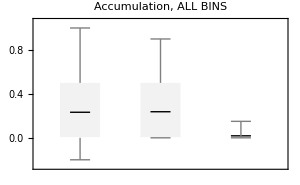
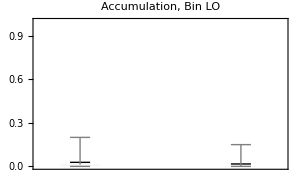
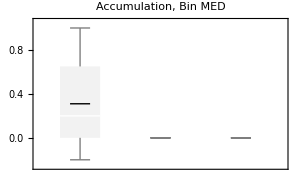
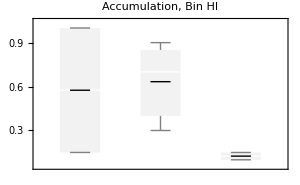

```mathematica
pBW = BoxWhiskerChart[{accumNTall⟦All,2⟧,accumTLall⟦All,2⟧,accumTAall⟦All,2⟧},"Mean",ChartStyle->Lighter[Gray,0.9], ImageSize->300,PlotLabel-> "Accumulation, ALL BINS"];
pBWL = BoxWhiskerChart[{accumNTL⟦All,2⟧,accumTLL⟦All,2⟧,accumTAL⟦All,2⟧},"Mean",ChartStyle->Lighter[Gray,0.9], ImageSize->300,PlotLabel-> "Accumulation, Bin LO", PlotRange -> {0,1}];
pBWM = BoxWhiskerChart[{accumNTM⟦All,2⟧,accumTLM⟦All,2⟧,accumTAM⟦All,2⟧},"Mean",ChartStyle->Lighter[Gray,0.9], ImageSize->300,PlotLabel-> "Accumulation, Bin MED"];
pBWH = BoxWhiskerChart[{accumNTH⟦All,2⟧,accumTLH⟦All,2⟧,accumTAH⟦All,2⟧},"Mean",ChartStyle->Lighter[Gray,0.9], ImageSize->300,PlotLabel-> "Accumulation, Bin HI"];
Row[{pBW, pBWL, pBWM, pBWH
}]
```

NT, TL, and TA accumulation% at 10h
The MEDIAN is represented as a black line. 
The MEAN of each is 0

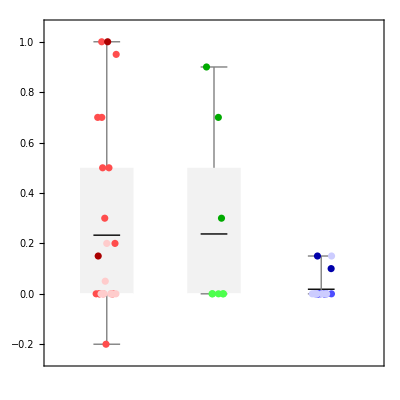

```mathematica
Row[{"NT, TL, and TA accumulation% at 10h
The MEDIAN is represented as a black line. 
The MEAN of each is 0"
}]
Row[{Show[pBW,paccumNT,paccumTL,paccumTA,AspectRatio->1,PlotRange->All  ]
}]
```

## Binning based on Accumulation in cell at frames 1-5

```mathematica
NTdata//Dimensions
TAdata//Dimensions
TLdata//Dimensions
```

{31,7,1}

{31,7,1}

{13,7,1}

```mathematica
NTdata =Join[myNT1,myNT2];
TAdata = Join[myTA1,myTA2];
TLdata = Join[myTL2];
```

```mathematica
(* 
TLdata = myTL2⟦4,Flatten@Position[myTL2⟦4⟧,""]⟧=0
```

```mathematica
rmNTdata = NTdata/.""->0.//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
rmTLdata = TLdata/.""->0.//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
rmTAdata = TAdata/.""->0.//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
```

```mathematica
(* USE THESE INSTEAD if you dont want to remove high accum data... 


NTdata0= NTdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;
NTdataL= NTdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]≤ .25]&;
NTdataM= NTdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤1.]&;
NTdataH= NTdata/.""->0.//Cases[#,x_/; 1.≤ Total[x⟦4,1,2;;6,2⟧]]&;
TAdata0= TAdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;
TAdataL= TAdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]≤ .25]&;
TAdataM= TAdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤ 1.]&;
TAdataH= TAdata/.""->0.//Cases[#,x_/; 1.≤Total[x⟦4,1,2;;6,2⟧]]&;
TLdata0= TLdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;
TLdataL= TLdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]<.25]&;
TLdataM= TLdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤1.]&;
TLdataH= TLdata/.""->0.//Cases[#,x_/; 1.≤Total[x⟦4,1,2;;6,2⟧]]&;
```

```mathematica
p = 1.5
NTdata0= rmNTdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;
NTdataL= rmNTdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]≤ .25]&;
NTdataM= rmNTdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤p]&;
NTdataH= rmNTdata/.""->0.//Cases[#,x_/; p≤ Total[x⟦4,1,2;;6,2⟧]]&;
TAdata0= rmTAdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;TAdataL= rmTAdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]≤ .25]&;
TAdataM= rmTAdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤ 1p]&;
TAdataH= rmTAdata/.""->0.//Cases[#,x_/; p≤Total[x⟦4,1,2;;6,2⟧]]&;
TLdata0= rmTLdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;TLdataL= rmTLdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]<.25]&;
TLdataM= rmTLdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤p]&;
TLdataH= rmTLdata/.""->0.//Cases[#,x_/; p≤Total[x⟦4,1,2;;6,2⟧]]&;
```

1.5

```mathematica
Table[Total[TLdata[[j,4,1,2;;6,2]]],{j,1,Length@TLdata,1}]
```

{0.+3 ,0.+3 ,1.9,2.6,0.,0.+3 ,0.+,0.2,0.+,4 +f,0.05,0.7,0.05+4 }

```mathematica
(*
NTdata0=NTdata//Cases[#,x_/; Head[Total[x[[4,1,2;;6,2]]]]== Plus]&;
NTdataL=Cases[NTdata,x_/; Total[x[[4,1,2;;6,2]]]<.25];
NTdataL=Cases[NTdata,x_/; Total[x[[4,1,2;;6,2]]]<.25];
NTdataM=Cases[NTdata,x_/; .25≤Total[x[[4,1,2;;6,2]]]≤.75];
NTdataH=Cases[NTdata,x_/; 75≤Total[x[[4,1,2;;6,2]]]];
TAdata0=Cases[TAdata,x_/; Head[Total[x[[4,1,2;;6,2]]]]== Plus];TAdataL=Cases[TAdata,x_/; Total[x[[4,1,2;;6,2]]]<.25];
TAdataM=Cases[TAdata,x_/; .25≤Total[x[[4,1,2;;6,2]]]<.75];
TAdataH=Cases[TAdata,x_/; 75≤Total[x[[4,1,2;;6,2]]]];
TLdata0=TLdata//Cases[3,x_/; Head[Total[x[[4,1,2;;6,2]]]]== Plus]&;TLdataL=Cases[TLdata,x_/; 0≤Total[x[[4,1,2;;6,2]]]<.25];
TLdataM=Cases[TLdata,x_/; .25≤Total[x[[4,1,2;;6,2]]]≤.75];
TLdataH=Cases[TLdata,x_/; .75≤Total[x[[4,1,2;;6,2]]]];
```

```mathematica
Row[{"TA  ",Length@TAdata ," " ,Length@TAdata0," " ,Length@TAdataL ," " ,Length@TAdataM ," " ,Length@TAdataH}]
Row[{"NT  ",Length@NTdata ," " ,Length@NTdata0," " ,Length@NTdataL ," " ,Length@NTdataM ," " ,Length@NTdataH}]
Row[{"TL  ",Length@TLdata ," " ,Length@TLdata0," " ,Length@TLdataL ," " ,Length@TLdataM ," " ,Length@TLdataH}]
```

TA  31 0 24 4 2

NT  31 0 13 5 14

TL  13 0 9 1 2

TA  31 0 24 4 2

NT  31 0 13 7 13

TL  13 0 9 1 2

### Graphs...

#### RNA :

```mathematica
prnaTAL = 
TAdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTAM = 
TAdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTAH = 
TAdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
```

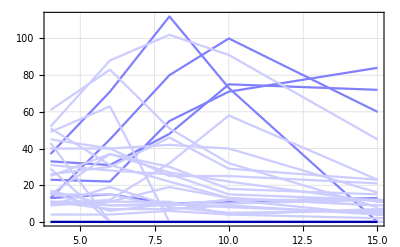

```mathematica
prnaTA = Show[prnaTAM,prnaTAL, prnaTAH]
```

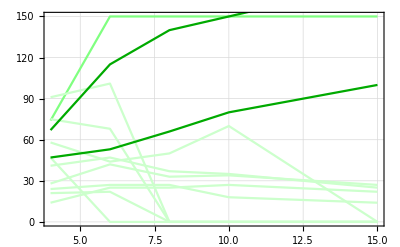

```mathematica
prnaTLL = 
TLdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTLM = 
TLdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTLH = 
TLdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTL = Show[prnaTLM,prnaTLL, prnaTLH]
```

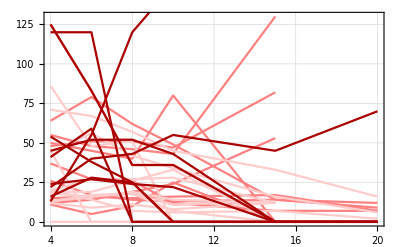

```mathematica
prnaNTL = 
NTdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNTM = 
NTdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNTH = 
NTdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNT = Show[prnaNTM,prnaNTL, prnaNTH]
```

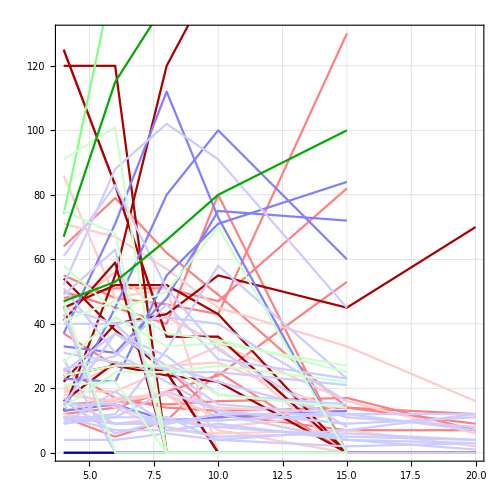

```mathematica
Show[prnaNT,prnaTA,prnaTL,AspectRatio->1]
```

#### %Translation :

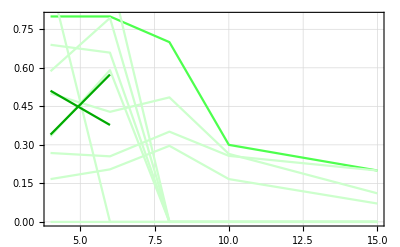

```mathematica
ptransTLL=TLdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTLM=TLdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTLH=TLdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTL = Show[ptransTLM,ptransTLL, ptransTLH]
```

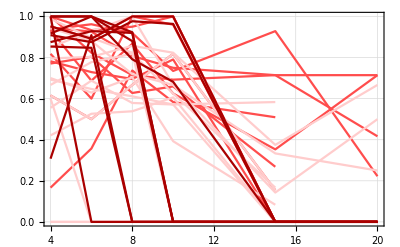

```mathematica
ptransNTL=NTdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNTM=NTdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNTH=NTdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNT = Show[ptransNTM,ptransNTL, ptransNTH]
```

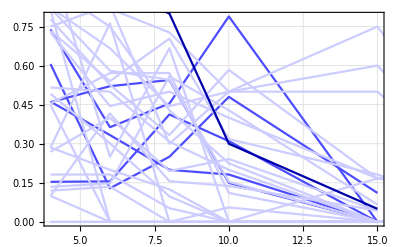

```mathematica
ptransTAL=TAdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTAM=TAdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTAH=TAdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTA = Show[ptransTAM,ptransTAL, ptransTAH]
```

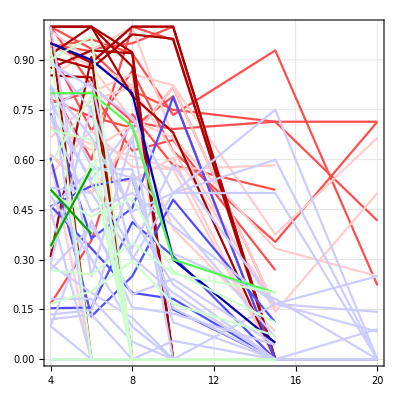

```mathematica
Show[ptransNT,ptransTA,ptransTL,AspectRatio->1]
```

#### # Tethered :

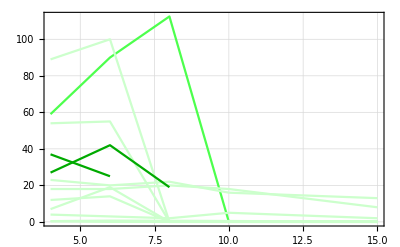

```mathematica
ptethTLL=TLdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTLM=TLdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTLH=TLdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTL = Show[ptethTLM,ptethTLL, ptethTLH]
```

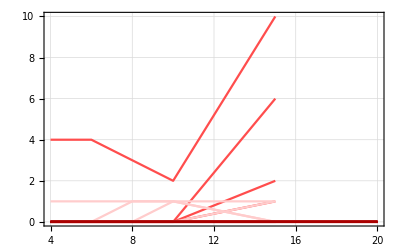

```mathematica
ptethNTL=NTdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNTM=NTdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNTH=NTdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNT = Show[ptethNTM,ptethNTL, ptethNTH]
```

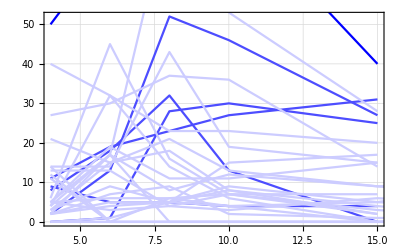

```mathematica
ptethTAL=TAdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTAM=TAdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTAH=TAdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Blue,Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTA = Show[ptethTAM,ptethTAL, ptethTAH]
```

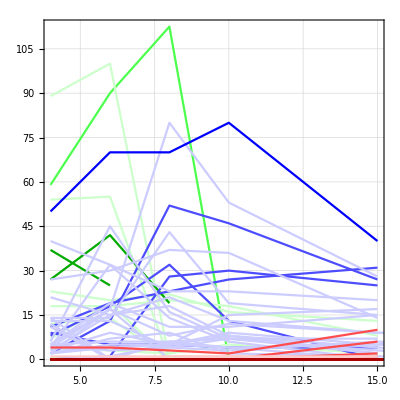

```mathematica
Show[ptethTL,ptethTA,ptethNT,AspectRatio->1]
```

#### % cy3 accumulation :

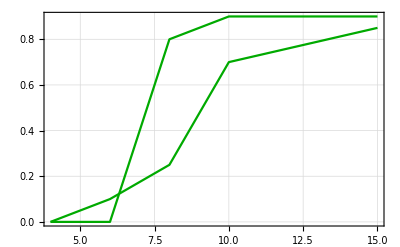

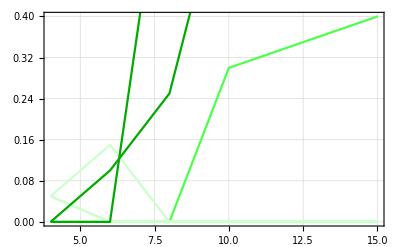

```mathematica
paccumTLL=TLdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTLM=TLdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTLH=TLdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
paccumTL = Show[paccumTLM,paccumTLL, paccumTLH]
```

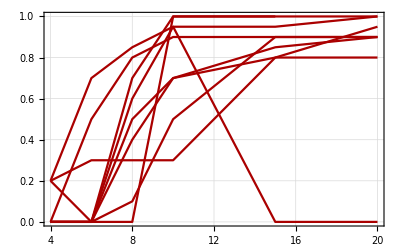

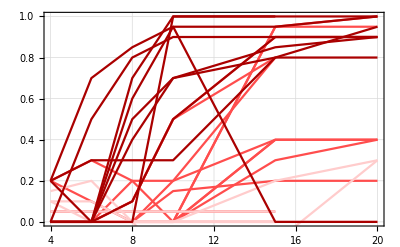

```mathematica
paccumNTL=NTdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumNTM=NTdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumNTH=NTdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
paccumNT = Show[paccumNTM,paccumNTL, paccumNTH]
```

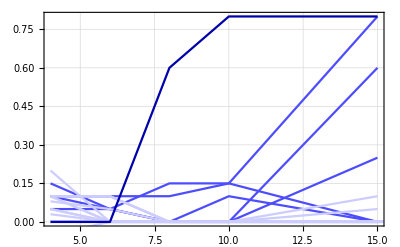

```mathematica
paccumTAL=TAdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTAM=TAdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTAH=TAdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTA = Show[paccumTAM,paccumTAL, paccumTAH]
```

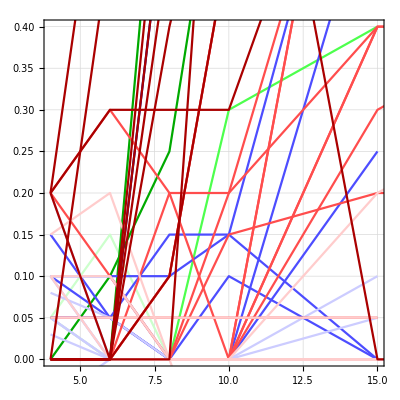

```mathematica
Show[paccumTL,paccumTA,paccumNT,AspectRatio->1]
```

#### Totals :

Binned by % accumulation: <25%,  25-75%,  >75%

TA  31   inc 0   lo 24   med 5   hi 1

NT  31   inc 0   lo 13   med 11   hi 9

TL  13   inc 0   lo 9    med 1    hi 2

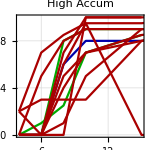
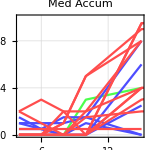
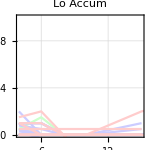

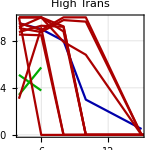
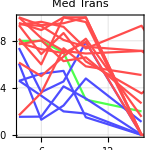
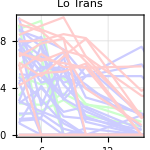

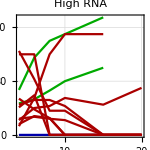
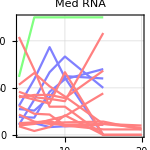

***NOTE, the drop to 0 is sometimes bc the cell can't be quantified anymore! 
***NOT biologically relevant, not actually happening!

```mathematica
Row[{"Binned by % accumulation: <25%,  25-75%,  >75%"}]
Row[{"TA  ",Length@TAdata ,"   inc " ,Length@TAdata0,"   lo " ,Length@TAdataL ,"   med " ,Length@TAdataM ,"   hi " ,Length@TAdataH}]
Row[{"NT  ",Length@NTdata ,"   inc " ,Length@NTdata0,"   lo " ,Length@NTdataL ,"   med " ,Length@NTdataM ,"   hi " ,Length@NTdataH}]
Row[{"TL  ",Length@TLdata ,"   inc " ,Length@TLdata0,"   lo " ,Length@TLdataL ,"    med " ,Length@TLdataM ,"    hi " ,Length@TLdataH}]
Row[{Show[paccumTLH,paccumTAH,paccumNTH,AspectRatio->1,PlotLabel->"High Accum",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[paccumTLM,paccumTAM,paccumNTM,AspectRatio->1,PlotLabel->"Med Accum",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[paccumTLL,paccumTAL,paccumNTL,AspectRatio->1,PlotLabel->"Lo Accum",PlotRange->{{4,15},{0,1}},ImageSize->150]
}]
Row[{Show[ptransTLH,ptransTAH,ptransNTH,AspectRatio->1,PlotLabel->"High Trans",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[ptransTLM,ptransTAM,ptransNTM,AspectRatio->1,PlotLabel->"Med Trans",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[ptransTLL,ptransTAL,ptransNTL,AspectRatio->1,PlotLabel->"Lo Trans",PlotRange->{{4,15},{0,1}},ImageSize->150]
}]
Row[{Show[prnaTLH,prnaTAH,prnaNTH,AspectRatio->1,PlotLabel->"High RNA",PlotRange->{{4,15},{0,All}},ImageSize->150],
Show[prnaTLM,prnaTAM,prnaNTM,AspectRatio->1,PlotLabel->"Med RNA",PlotRange->{{4,15},{0,All}},ImageSize->150],
Show[prnaTLL,prnaTAL,prnaNTL,AspectRatio->1,PlotLabel->"Lo RNA",PlotRange->{{4,15},{0,All}},ImageSize->150]
}]
Row[{"***NOTE, the drop to 0 is sometimes bc the cell can't be quantified anymore! 
***NOT biologically relevant, not actually happening!"}]
```

NOTE!!! This is neglecting that since I’m doing the total I’m not actually 
doing 50-75% or over 75% or whatever, I’m totalling multiple points!!!

## Binning based on Accumulation in cell at frames 1-5 WITH BoxWhisk charts

```mathematica
NTdata//Dimensions
TAdata//Dimensions
TLdata//Dimensions
```

{31,7,1}

{31,7,1}

{13,7,1}

```mathematica
NTdata =Join[myNT1,myNT2];
TAdata = Join[myTA1,myTA2];
TLdata = Join[myTL2];
```

```mathematica
(* 
TLdata = myTL2⟦4,Flatten@Position[myTL2⟦4⟧,""]⟧=0
```

```mathematica
rmNTdata = NTdata/.""->0.//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
rmTLdata = TLdata/.""->0.//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
rmTAdata = TAdata/.""->0.//Cases[#,x_/; x⟦4,1,2,2⟧≤ .2]&;
```

```mathematica
(* USE THESE INSTEAD if you dont want to remove high accum data... 


NTdata0= NTdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;
NTdataL= NTdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]≤ .25]&;
NTdataM= NTdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤1.]&;
NTdataH= NTdata/.""->0.//Cases[#,x_/; 1.≤ Total[x⟦4,1,2;;6,2⟧]]&;
TAdata0= TAdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;
TAdataL= TAdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]≤ .25]&;
TAdataM= TAdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤ 1.]&;
TAdataH= TAdata/.""->0.//Cases[#,x_/; 1.≤Total[x⟦4,1,2;;6,2⟧]]&;
TLdata0= TLdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;
TLdataL= TLdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]<.25]&;
TLdataM= TLdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤1.]&;
TLdataH= TLdata/.""->0.//Cases[#,x_/; 1.≤Total[x⟦4,1,2;;6,2⟧]]&;
```

```mathematica
p = 1.5
NTdata0= rmNTdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;
NTdataL= rmNTdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]≤ .25]&;
NTdataM= rmNTdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤p]&;
NTdataH= rmNTdata/.""->0.//Cases[#,x_/; p≤ Total[x⟦4,1,2;;6,2⟧]]&;
TAdata0= rmTAdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;TAdataL= rmTAdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]≤ .25]&;
TAdataM= rmTAdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤ 1p]&;
TAdataH= rmTAdata/.""->0.//Cases[#,x_/; p≤Total[x⟦4,1,2;;6,2⟧]]&;
TLdata0= rmTLdata/.""->0.//Cases[#,x_/; Head[Total[x⟦4,1,2;;6,2⟧]]== Plus]&;TLdataL= rmTLdata/.""->0.//Cases[#,x_/; Total[x⟦4,1,2;;6,2⟧]<.25]&;
TLdataM= rmTLdata/.""->0.//Cases[#,x_/; .25≤Total[x⟦4,1,2;;6,2⟧]≤p]&;
TLdataH= rmTLdata/.""->0.//Cases[#,x_/; p≤Total[x⟦4,1,2;;6,2⟧]]&;
```

1.5

```mathematica
Table[Total[TLdata[[j,4,1,2;;6,2]]],{j,1,Length@TLdata,1}]
```

{0.+3 ,0.+3 ,1.9,2.6,0.,0.+3 ,0.+,0.2,0.+,4 +f,0.05,0.7,0.05+4 }

```mathematica
(*
NTdata0=NTdata//Cases[#,x_/; Head[Total[x[[4,1,2;;6,2]]]]== Plus]&;
NTdataL=Cases[NTdata,x_/; Total[x[[4,1,2;;6,2]]]<.25];
NTdataL=Cases[NTdata,x_/; Total[x[[4,1,2;;6,2]]]<.25];
NTdataM=Cases[NTdata,x_/; .25≤Total[x[[4,1,2;;6,2]]]≤.75];
NTdataH=Cases[NTdata,x_/; 75≤Total[x[[4,1,2;;6,2]]]];
TAdata0=Cases[TAdata,x_/; Head[Total[x[[4,1,2;;6,2]]]]== Plus];TAdataL=Cases[TAdata,x_/; Total[x[[4,1,2;;6,2]]]<.25];
TAdataM=Cases[TAdata,x_/; .25≤Total[x[[4,1,2;;6,2]]]<.75];
TAdataH=Cases[TAdata,x_/; 75≤Total[x[[4,1,2;;6,2]]]];
TLdata0=TLdata//Cases[3,x_/; Head[Total[x[[4,1,2;;6,2]]]]== Plus]&;TLdataL=Cases[TLdata,x_/; 0≤Total[x[[4,1,2;;6,2]]]<.25];
TLdataM=Cases[TLdata,x_/; .25≤Total[x[[4,1,2;;6,2]]]≤.75];
TLdataH=Cases[TLdata,x_/; .75≤Total[x[[4,1,2;;6,2]]]];
```

```mathematica
Row[{"TA  ",Length@TAdata ," " ,Length@TAdata0," " ,Length@TAdataL ," " ,Length@TAdataM ," " ,Length@TAdataH}]
Row[{"NT  ",Length@NTdata ," " ,Length@NTdata0," " ,Length@NTdataL ," " ,Length@NTdataM ," " ,Length@NTdataH}]
Row[{"TL  ",Length@TLdata ," " ,Length@TLdata0," " ,Length@TLdataL ," " ,Length@TLdataM ," " ,Length@TLdataH}]
```

TA  31 0 24 4 2

NT  31 0 13 5 14

TL  13 0 9 1 2

TA  31 0 24 4 2

NT  31 0 13 7 13

TL  13 0 9 1 2

### Graphs...

#### RNA :

```mathematica
prnaTAL = 
TAdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTAM = 
TAdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTAH = 
TAdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
```

```mathematica
prnaTA = Show[prnaTAM,prnaTAL, prnaTAH]
```

-Graphics-

```mathematica
prnaTLL = 
TLdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTLM = 
TLdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTLH = 
TLdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaTL = Show[prnaTLM,prnaTLL, prnaTLH]
```

-Graphics-

```mathematica
prnaNTL = 
NTdataL[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNTM = 
NTdataM[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.5],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNTH = 
NTdataH[[All,2,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
prnaNT = Show[prnaNTM,prnaNTL, prnaNTH]
```

-Graphics-

```mathematica
Show[prnaNT,prnaTA,prnaTL,AspectRatio->1]
```

-Graphics-

#### %Translation :

```mathematica
ptransTLL=TLdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTLM=TLdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTLH=TLdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTL = Show[ptransTLM,ptransTLL, ptransTLH]
```

-Graphics-

```mathematica
ptransNTL=NTdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNTM=NTdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNTH=NTdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransNT = Show[ptransNTM,ptransNTL, ptransNTH]
```

-Graphics-

```mathematica
ptransTAL=TAdataL[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTAM=TAdataM[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTAH=TAdataH[[All,3,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptransTA = Show[ptransTAM,ptransTAL, ptransTAH]
```

-Graphics-

```mathematica
Show[ptransNT,ptransTA,ptransTL,AspectRatio->1]
```

-Graphics-

#### # Tethered :

```mathematica
ptethTLL=TLdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTLM=TLdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTLH=TLdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTL = Show[ptethTLM,ptethTLL, ptethTLH]
```

-Graphics-

```mathematica
ptethNTL=NTdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNTM=NTdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNTH=NTdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethNT = Show[ptethNTM,ptethNTL, ptethNTH]
```

-Graphics-

```mathematica
ptethTAL=TAdataL[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTAM=TAdataM[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTAH=TAdataH[[All,7,1,2;;All]]//ListPlot[#,PlotStyle->Blue,Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
ptethTA = Show[ptethTAM,ptethTAL, ptethTAH]
```

-Graphics-

```mathematica
Show[ptethTL,ptethTA,ptethNT,AspectRatio->1]
```

-Graphics-

#### % cy3 accumulation :

```mathematica
paccumTLL=TLdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTLM=TLdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTLH=TLdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
paccumTL = Show[paccumTLM,paccumTLL, paccumTLH]
```

-Graphics-

-Graphics-

```mathematica
paccumNTL=NTdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumNTM=NTdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Red,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumNTH=NTdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Red],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
paccumNT = Show[paccumNTM,paccumNTL, paccumNTH]
```

-Graphics-

-Graphics-

```mathematica
paccumTAL=TAdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTAM=TAdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Blue,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTAH=TAdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Blue],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTA = Show[paccumTAM,paccumTAL, paccumTAH]
```

-Graphics-

```mathematica
Show[paccumTL,paccumTA,paccumNT,AspectRatio->1]
```

-Graphics-

#### Totals :

```mathematica
Row[{"Binned by % accumulation: <25%,  25-75%,  >75%"}]
Row[{"TA  ",Length@TAdata ,"   inc " ,Length@TAdata0,"   lo " ,Length@TAdataL ,"   med " ,Length@TAdataM ,"   hi " ,Length@TAdataH}]
Row[{"NT  ",Length@NTdata ,"   inc " ,Length@NTdata0,"   lo " ,Length@NTdataL ,"   med " ,Length@NTdataM ,"   hi " ,Length@NTdataH}]
Row[{"TL  ",Length@TLdata ,"   inc " ,Length@TLdata0,"   lo " ,Length@TLdataL ,"    med " ,Length@TLdataM ,"    hi " ,Length@TLdataH}]
Row[{Show[paccumTLH,paccumTAH,paccumNTH,AspectRatio->1,PlotLabel->"High Accum",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[paccumTLM,paccumTAM,paccumNTM,AspectRatio->1,PlotLabel->"Med Accum",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[paccumTLL,paccumTAL,paccumNTL,AspectRatio->1,PlotLabel->"Lo Accum",PlotRange->{{4,15},{0,1}},ImageSize->150]
}]
Row[{Show[ptransTLH,ptransTAH,ptransNTH,AspectRatio->1,PlotLabel->"High Trans",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[ptransTLM,ptransTAM,ptransNTM,AspectRatio->1,PlotLabel->"Med Trans",PlotRange->{{4,15},{0,1}},ImageSize->150],
Show[ptransTLL,ptransTAL,ptransNTL,AspectRatio->1,PlotLabel->"Lo Trans",PlotRange->{{4,15},{0,1}},ImageSize->150]
}]
Row[{Show[prnaTLH,prnaTAH,prnaNTH,AspectRatio->1,PlotLabel->"High RNA",PlotRange->{{4,15},{0,All}},ImageSize->150],
Show[prnaTLM,prnaTAM,prnaNTM,AspectRatio->1,PlotLabel->"Med RNA",PlotRange->{{4,15},{0,All}},ImageSize->150],
Show[prnaTLL,prnaTAL,prnaNTL,AspectRatio->1,PlotLabel->"Lo RNA",PlotRange->{{4,15},{0,All}},ImageSize->150]
}]
Row[{"***NOTE, the drop to 0 is sometimes bc the cell can't be quantified anymore! 
***NOT biologically relevant, not actually happening!"}]
```

Binned by % accumulation: <25%,  25-75%,  >75%

TA  31   inc 0   lo 24   med 5   hi 1

NT  31   inc 0   lo 13   med 11   hi 9

TL  13   inc 0   lo 9    med 1    hi 2

-Graphics--Graphics--Graphics-

-Graphics--Graphics--Graphics-

-Graphics--Graphics--Graphics-

***NOTE, the drop to 0 is sometimes bc the cell can't be quantified anymore! 
***NOT biologically relevant, not actually happening!

NOTE!!! This is neglecting that since I’m doing the total I’m not actually 
doing 50-75% or over 75% or whatever, I’m totalling multiple points!!!

### Determine point of accumulation getting above 50% ***use this to show TIME when cell accumulated product ****ALL DEV!!!!!****

```mathematica
paccumTLL=TLdataL[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.8],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTLM=TLdataM[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Lighter[Green,.3],Joined->True,PlotTheme->"Detailed",PlotRange->All]&;
paccumTLH=TLdataH[[All,4,1,2;;All]]//ListPlot[#,PlotStyle->Darker[Green],Joined->True,PlotTheme->"Detailed",PlotRange->All]&
paccumTL = Show[paccumTLM,paccumTLL, paccumTLH]
```

```mathematica
Cases[TLdata,x_/; Head[x⟦p,1,o,2⟧]== String]
```

Part::partd: Part specification {{TL05},{{{hours,#RNA},{4.,91.},{6.,101.},{8.,},{10.,},{15.,}}},{{{hours,%Translating},{4.,0.901099},{6.,0.970297},{8.,},{10.,},{15.,}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,},{10.,},{15.,}}},{{{hours,Sick? (T/F) },{4.,f},{6.,f},{8.,dead},{10.,dead},{15.,dead}}},{{{hours,AGO},{4.,2.},{6.,2.5},{8.,},{10.,},{15.,}}},{{{hours,Tethering?},{4.,89.},{6.,100.},{8.,},{10.,},{15.,}}}}⟦0,1,4,2⟧ is longer than depth of object.

Part::partd: Part specification {{TL04},{{{hours,#RNA},{4.,21.},{6.,22.},{8.,},{10.,},{15.,}}},{{{hours,%Translating},{4.,0.333333},{6.,0.590909},{8.,},{10.,},{15.,}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,},{10.,},{15.,}}},{{{hours,Sick? (T/F) },{4.,f},{6.,f},{8.,dead},{10.,dead},{15.,dead}}},{{{hours,AGO},{4.,0.},{6.,1.},{8.,},{10.,},{15.,}}},{{{hours,Tethering?},{4.,7.},{6.,19.},{8.,},{10.,},{15.,}}}}⟦0,1,4,2⟧ is longer than depth of object.

Part::partd: Part specification {{TL12},{{{hours,#RNA},{4.,67.},{6.,115.},{8.,140.},{10.,150.},{15.,175.}}},{{{hours,%Translating},{4.,0.34},{6.,0.573913},{8.,na},{10.,na},{15.,na}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.1},{8.,0.25},{10.,0.7},{15.,0.85}}},{{{hours,Sick? (T/F) },{4.,f},{6.,f},{8.,f},{10.,t},{15.,t}}},{{{hours,AGO},{4.,1.},{6.,2.},{8.,3.},{10.,3.},{15.,3.}}},{{{hours,Tethering?},{4.,37.},{6.,25.},{8.,na},{10.,na},{15.,na}}}}⟦0,1,4,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{}

```mathematica
Cases[TLdataH[[4,1,1;;All,2]],x_/;x≥.5]
```

Part::partw: Part 4 of … does not exist.

{4,1,2}

```mathematica
TLdataH[[All,4,1,1;;All,2]]
```

{{Cy3 Accum (%),0.,0.1,0.25,0.7,0.85},{Cy3 Accum (%),0.,0.,0.8,0.9,0.9}}

```mathematica
p = 4;
TLdataH//Cases[#,x_/;  x⟦p,1,2;;All,2⟧≥ .5]&
```

{}

```mathematica
Number
```

```mathematica
Table[NTdataH[[All,4,1,2;;All]],{i,1,1,1}]
```

{{{{4.,0.},{6.,0.},{8.,0.},{10.,1.},{15.,1.},{20.,1.}},{{4.,0.2},{6.,0.3},{8.,0.3},{10.,0.3},{15.,0.8},{20.,0.95}},{{4.,0.2},{6.,0.},{8.,0.6},{10.,0.95},{15.,0.},{20.,0.}},{{4.,0.2},{6.,0.7},{8.,0.85},{10.,0.95},{15.,0.95},{20.,1.}},{{4.,0.},{6.,0.5},{8.,0.8},{10.,0.9},{15.,0.9},{20.,0.9}},{{4.,0.},{6.,0.},{8.,0.1},{10.,0.5},{15.,0.9},{20.,0.9}},{{4.,0.},{6.,0.},{8.,0.5},{10.,0.7},{15.,0.8},{20.,0.8}},{{4.,0.},{6.,0.},{8.,0.4},{10.,0.7},{15.,0.85},{20.,0.9}},{{4.,0.},{6.,0.},{8.,0.7},{10.,1.},{15.,1.}}}}

```mathematica
NTdataH[[All,4,1,2;;6]]//TableForm
```

4.
0. | 6.
0. | 8.
0. | 10.
1. | 15.
1.
4.
0.2 | 6.
0.3 | 8.
0.3 | 10.
0.3 | 15.
0.8
4.
0.2 | 6.
0. | 8.
0.6 | 10.
0.95 | 15.
0.
4.
0.2 | 6.
0.7 | 8.
0.85 | 10.
0.95 | 15.
0.95
4.
0. | 6.
0.5 | 8.
0.8 | 10.
0.9 | 15.
0.9
4.
0. | 6.
0. | 8.
0.1 | 10.
0.5 | 15.
0.9
4.
0. | 6.
0. | 8.
0.5 | 10.
0.7 | 15.
0.8
4.
0. | 6.
0. | 8.
0.4 | 10.
0.7 | 15.
0.85
4.
0. | 6.
0. | 8.
0.7 | 10.
1. | 15.
1.

```mathematica
NTdataH[[All,4,1,2;;6]]//Cases[#,x_/; x⟦1,2⟧>0]&//TableForm
```

4.
0.2 | 6.
0.3 | 8.
0.3 | 10.
0.3 | 15.
0.8
4.
0.2 | 6.
0. | 8.
0.6 | 10.
0.95 | 15.
0.
4.
0.2 | 6.
0.7 | 8.
0.85 | 10.
0.95 | 15.
0.95

```mathematica
Table[NTdataH⟦4,1,i,2⟧>0,{i,2,6,1}]
```

{False,False,False,True,True}

```mathematica
NTdataH[[All,4]]
```

{{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.},{10.,1.},{15.,1.},{20.,1.}}},{{{hours,Cy3 Accum (%)},{4.,0.2},{6.,0.3},{8.,0.3},{10.,0.3},{15.,0.8},{20.,0.95}}},{{{hours,Cy3 Accum (%)},{4.,0.2},{6.,0.},{8.,0.6},{10.,0.95},{15.,0.},{20.,0.}}},{{{hours,Cy3 Accum (%)},{4.,0.2},{6.,0.7},{8.,0.85},{10.,0.95},{15.,0.95},{20.,1.}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.5},{8.,0.8},{10.,0.9},{15.,0.9},{20.,0.9}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.1},{10.,0.5},{15.,0.9},{20.,0.9}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.5},{10.,0.7},{15.,0.8},{20.,0.8}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.4},{10.,0.7},{15.,0.85},{20.,0.9}}},{{{hours,Cy3 Accum (%)},{4.,0.},{6.,0.},{8.,0.7},{10.,1.},{15.,1.}}}}

0.5

```mathematica
rmTLdata[[All,4,1,2;;All]]
```

{{{4.,0.},{6.,0.},{8.,},{10.,},{15.,}},{{4.,0.},{6.,0.},{8.,},{10.,},{15.,}},{{4.,0.},{6.,0.1},{8.,0.25},{10.,0.7},{15.,0.85}},{{4.,0.},{6.,0.},{8.,0.8},{10.,0.9},{15.,0.9}},{{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,0.}},{{4.,0.},{6.,0.},{8.,},{10.,},{15.,}},{{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,}},{{4.,0.05},{6.,0.15},{8.,0.},{10.,0.},{15.,0.}},{{4.,0.},{6.,0.},{8.,0.},{10.,0.},{15.,}},{{4.,0.05},{6.,0.},{8.,0.},{10.,0.},{15.,0.}},{{4.,0.},{6.,0.},{8.,0.},{10.,0.3},{15.,0.4}},{{4.,0.05},{6.,},{8.,},{10.,},{15.,}}}

```mathematica
Dimensions/@rmTLdata
```

{{7,1},{7,1},{7,1},{7,1},{7,1},{7,1},{7,1},{7,1},{7,1},{7,1},{7,1},{7,1}}

```mathematica
p = 0;
Cases[rmTLdata,x_/; AnyTrue[p≤  Table[x⟦4,1,i,2⟧,{i,2,6,1}]]]
```

```mathematica
Cases[rmTLdata,x_/; AnyTrue[p≤  x⟦4,1,2;;All,2⟧]]
```

{}

```mathematica
AnyTrue[p≤  rmTLdata⟦All,4,1,2;;All,2⟧]
```

AnyTrue[0≤{{0.,0.,,,},{0.,0.,,,},{0.,0.1,0.25,0.7,0.85},{0.,0.,0.8,0.9,0.9},{0.,0.,0.,0.,0.},{0.,0.,,,},{0.,0.,0.,0.,},{0.05,0.15,0.,0.,0.},{0.,0.,0.,0.,},{0.05,0.,0.,0.,0.},{0.,0.,0.,0.3,0.4},{0.05,,,,}}]

```mathematica
temp =  rmTLdata⟦All,4,1,2;;All,2⟧
```

{{0.,0.,,,},{0.,0.,,,},{0.,0.1,0.25,0.7,0.85},{0.,0.,0.8,0.9,0.9},{0.,0.,0.,0.,0.},{0.,0.,,,},{0.,0.,0.,0.,},{0.05,0.15,0.,0.,0.},{0.,0.,0.,0.,},{0.05,0.,0.,0.,0.},{0.,0.,0.,0.3,0.4},{0.05,,,,}}

### Graph the %accumulation at 10h for HML w a scatter plot

```mathematica
accumNTL= Table[NTdataL[[i,4,1,5]]/. 10.->RandomReal[{.9,1.1}],{i,1,Length@NTdataL,1}];
accumNTM= Table[NTdataM[[i,4,1,5]]/. 10.->RandomReal[{.9,1.1}],{i,1,Length@NTdataM,1}];
accumNTH= Table[NTdataH[[i,4,1,5]]/. 10.->RandomReal[{.9,1.1}],{i,1,Length@NTdataH,1}];accumTLL= Table[TLdataL[[i,4,1,5]]/. 10.->RandomReal[{1.9,2.1}],{i,1,Length@TLdataL,1}];
accumTLM= Table[TLdataM[[i,4,1,5]]/. 10.->RandomReal[{1.9,2.1}],{i,1,Length@TLdataM,1}];
accumTLH= Table[TLdataH[[i,4,1,5]]/. 10.->RandomReal[{1.9,2.1}],{i,1,Length@TLdataH,1}];
accumTAL= Table[TAdataL[[i,4,1,5]]/. 10.->RandomReal[{2.9,3.1}],{i,1,Length@TAdataL,1}];
accumTAM= Table[TAdataM[[i,4,1,5]]/. 10.->RandomReal[{2.9,3.1}],{i,1,Length@TAdataM,1}];
accumTAH= Table[TAdataH[[i,4,1,5]]/. 10.->RandomReal[{2.9,3.1}],{i,1,Length@TAdataH,1}];
```

```mathematica
accumTLall = Join[accumTLL, accumTLM, accumTLH];
accumTAall = Join[accumTAL, accumTAM, accumTAH];
accumNTall = Join[accumNTL, accumNTM, accumNTH];
```

#### % cy3 accumulation :

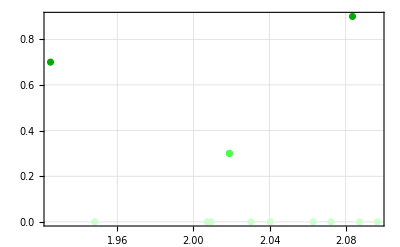

```mathematica
paccumTLL=accumTLL//ListPlot[#,PlotStyle->Lighter[Green,.8],PlotTheme->"Detailed",PlotRange->All]&;
paccumTLM=accumTLM//ListPlot[#,PlotStyle->Lighter[Green,.3],PlotTheme->"Detailed",PlotRange->All]&;
paccumTLH=accumTLH//ListPlot[#,PlotStyle->Darker[Green],PlotTheme->"Detailed",PlotRange->All]&;
paccumTL = Show[paccumTLM,paccumTLL, paccumTLH,PlotRange-> All]
```

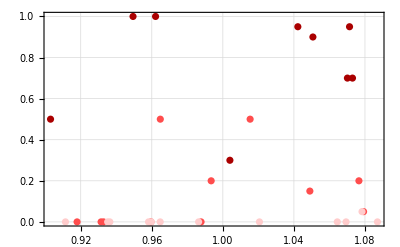

```mathematica
paccumNTL=accumNTL//ListPlot[#,PlotStyle->Lighter[Red,.8],PlotTheme->"Detailed",PlotRange->All]&;
paccumNTM=accumNTM//ListPlot[#,PlotStyle->Lighter[Red,.3],PlotTheme->"Detailed",PlotRange->All]&;
paccumNTH=accumNTH//ListPlot[#,PlotStyle->Darker[Red],PlotTheme->"Detailed",PlotRange->All]&;
paccumNT = Show[paccumNTM,paccumNTL, paccumNTH, PlotRange-> {0,1}]
```

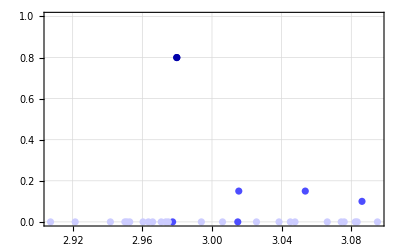

```mathematica
paccumTAL=accumTAL//ListPlot[#,PlotStyle->Lighter[Blue,.8],PlotTheme->"Detailed",PlotRange->All]&;
paccumTAM=accumTAM//ListPlot[#,PlotStyle->Lighter[Blue,.3],PlotTheme->"Detailed",PlotRange->All]&;
paccumTAH=accumTAH//ListPlot[#,PlotStyle->Darker[Blue],PlotTheme->"Detailed",PlotRange->All]&;
paccumTA = Show[paccumTAM,paccumTAL, paccumTAH,PlotRange-> {0,1}]
```

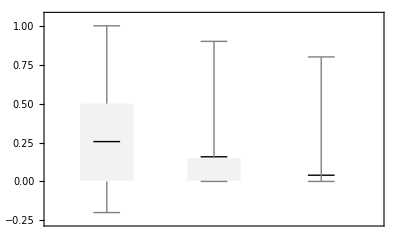

```mathematica
pBW = BoxWhiskerChart[{accumNTall⟦All,2⟧,accumTLall⟦All,2⟧,accumTAall⟦All,2⟧},"Mean",ChartStyle->Lighter[Gray,0.9], Axes]
```

NT, TL, and TA accumulation% at 10h
The MEDIAN is represented as a black line. 
The MEAN of each is 0

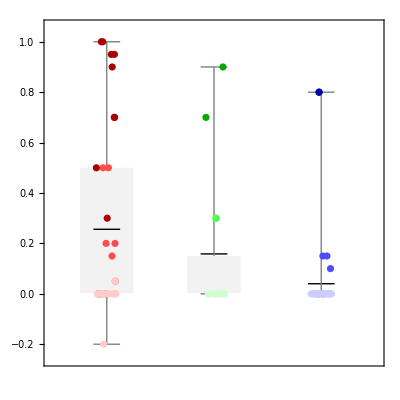

```mathematica
Row[{"NT, TL, and TA accumulation% at 10h
The MEDIAN is represented as a black line. 
The MEAN of each is 0"
}]
Row[{Show[pBW,paccumNT,paccumTL,paccumTA,AspectRatio->1,PlotRange->All]
}]
```

### Calculating the averages of replicate data set means....

```mathematica
Table[Mean[{AvgtethNT2[[i]],AvgtethNT1[[i]]}],{i,1,Length@AvgtethNT2,1}]
```

{}

```mathematica
Table[{AvgtethNT2[[i]],AvgtethNT1[[i]]},{i,1,Length@AvgtethNT2,1}]
```

{}

```mathematica
Mean/@Table[AvgtethNT2[i],{i,1,Length@AvgtethNT2,1}]
```

{}

```mathematica
totalAvgtethNT=Table[Mean[{AvgtethNT2[[i]],AvgtethNT1[[i]]}],{i,1,Length@AvgtethNT2,1}]
totalAvgtethNT//ListPlot[#,PlotStyle->{Darker[Red],Thickness[0.02]},Joined->True,PlotTheme->"Detailed",PlotMarkers->{Automatic,20}]&
```

{}

-Graphics-